Autocorrelations for Generalised Hybrid Monte Carlo

## Quadratic Operators with Exponentially Distributed Trajectories

Based on the paper, “Cost of the Generalised Hybrid Monte Carlo Algorithm for Free Field Theory”, this notebook contains a Mathematica format for selected equations. The aim is to provide a dynamic method of working with the theory.

The paper provides the Laplace Transform of the autocorrelations which will be denoted by F[...] where β is the Laplace transformed time, t

Unless explicitly stated, all equations are in Laplace Transformed format

Throughout the plots, the following parameters will be used:

```mathematica
τ = 0.1*20
```

2.

## Laplace Transformed GHMC Autocorrelation Function

The form is exceedingly long and so has been broken apart into testable segments specified by an[...],

```mathematica
a0[θ_,ρ_]:=-Cos[θ]^2+(1-2ρ)Cos[θ]+4
a1[θ_,ρ_] :=(-1+2ρ)Cos[θ]^3-3 Cos[θ]^2+(3-6ρ)Cos[θ]+6
a2[θ_,ρ_, ϕ_] :=(4ρ-2)Cos[θ]^3+((-2+2ρ)(ρ-2)ϕ^2+3-6ρ)Cos[θ] + ((4ρ-4)ϕ^2-3)Cos[θ]^2+(8-4ρ)ϕ^2+4
a3[θ_,ρ_, ϕ_] :=(4ρ-2)Cos[θ]^3+((4-4ρ)ϕ^2+3-6ρ)Cos[θ] + ((2ρ-4)ϕ^2-3)Cos[θ]^2+(8+2ρ)ϕ^2+4
a4[θ_,ρ_, ϕ_] :=(-4(-1+ρ)^2 ϕ^2-1+2ρ)Cos[θ]^3+((4ρ-4)ϕ^2-1)Cos[θ]^2+((-2+2ρ)(ρ-2)ϕ^2+1 -2ρ)Cos[θ] + (4-2ρ)ϕ^2+1
a5[θ_,ρ_, ϕ_] :=((2-2ρ)(ρ-2)ϕ^2-1+2ρ)Cos[θ]^3+(-4 ϕ^2-1)Cos[θ]^2+((-2ρ-4)(-1+ρ)ϕ^2+1-2ρ)Cos[θ]+(4ρ+4)ϕ^2+1
a6[θ_,ρ_, ϕ_] :=2ρ(-1+ρ)ϕ^2 Cos[θ]^3-2 Cos[θ]^2 ρ ϕ^2 - 2ρ(-1 + ρ)ϕ^2 Cos[θ]+2ρ ϕ^2
```

The Laplace Transform of the autocorrelation for quadratic operators is given by,

```mathematica
F[β_, ϕ_, θ_, ρ_, r_]:=(r β^4+a0[θ,ρ] r^2 β^3+(a1[θ,ρ]+(4-2ρ)ϕ^2)r^3 β^2 +a2[θ,ρ, ϕ] r^4 β+a4[θ,ρ, ϕ] r^5)/(β^5+a0[θ,ρ]r β^4+ (a1[θ,ρ]+4 ϕ^2)r^2 β^3 +a3[θ,ρ, ϕ] r^3 β^2+ a5[θ,ρ, ϕ] r^4 β + a6[θ,ρ, ϕ] r^5)
```

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
a7[θ_]:=-Cos[θ]+2-Cos[θ]^2
a8[θ_]:=Cos[θ]^3-Cos[θ]^2-Cos[θ]+1
```

```mathematica
Funit[β_, ϕ_, θ_, r_]:=(β^2 r+ β r^2 a7[θ] +r^3(Cos[θ]^3-Cos[θ]^2-Cos[θ]+2 ϕ^2+1))/(β^3+β^2 r a7[θ]+β r^2(a8[θ]+4 ϕ^2)+r^3(-2 Cos[θ]^2 ϕ^2+2 ϕ^2))
```

Check This should be equal to Equation (1) for ρ =1:

```mathematica
FullSimplify[Funit[β, ϕ, θ, r]==F[β, ϕ, θ, 1, r]]
```

True

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMC[β_,ϕ_, ρ_, r_]:= (β^2 r+ 2 r^2 β +  ϕ^2(4-2ρ)r^3 +r^3)/(β^3+2r β^2+(4 ϕ^2+1)r^2 β+2 r^3 ϕ^2 ρ)
```

Check This should be equal to Equation (1) for θ = π/2:

```mathematica
FullSimplify[F[β, 0, π/2, 0, 1]==FHMC[β,0,0, 1]]
```

True

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMCunit[β_, ϕ_, r_] :=(β^2 r+ 2β r^2 +2 r^3 ϕ^2+r^3)/(β^3+2 β^2 r+β r^2(1+4 ϕ^2)+r^3 2 ϕ^2)
```

Check This should be equal to Equation (1) for ρ = 1 and θ=π/2:

```mathematica
FullSimplify[FHMCunit[β, ϕ, r]==F[β, ϕ, π/2, 1, r]]
```

True

## Regular GHMC Integrated Autocorrelation Function

The integrated autocorrelation for GHMC is obtained by setting β = 0 for the autocorrelation in Equation (1). As it no longer contains a dependancy upon β, this is also equivalent to the Inverse Laplace Transform i.e. the non-Transformed Integrated Autocorrelation Function,

```mathematica
A[ϕ_, θ_, ρ_]:=a4[θ,ρ, ϕ]/a6[θ,ρ, ϕ]
```

Check This should be equal to Equation (1) for β=0:

```mathematica
FullSimplify[A[ϕ, θ, ρ] == F[0, ϕ, θ, ρ, r]]
```

True

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
Aunit[ϕ_, θ_]:=-(Cos[θ]^3-Cos[θ]^2-Cos[θ]+2 ϕ^2+1)/(2 ϕ^2(Cos[θ]^2-1))
```

Check This should be equal to Equation (1) for ρ=1 and β=0:

```mathematica
FullSimplify[Aunit[ϕ, θ]==F[0, ϕ, θ, 1, r]]
```

True

The integrated autocorrelation under unit acceptance varying with mixing angle,

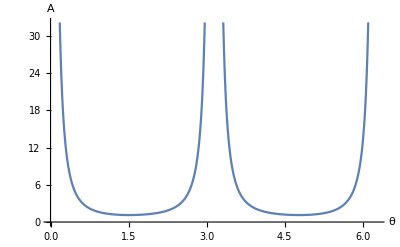

```mathematica
Plot[Aunit[τ, θ], {θ, 0, 2π},AxesLabel->{"θ","A"}]
```

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMC[ϕ_, ρ_]:=(2-ρ)/ρ+1/(2ρ ϕ^2)
```

Check This should be equal to Equation (1) for θ = π/2 and β=0:

```mathematica
FullSimplify[F[0,ϕ, π/2, ρ, r] == AHMC[ϕ, ρ]]
```

True

Showing the change in the HMC integrated autocorrelation varying with acceptance rate,

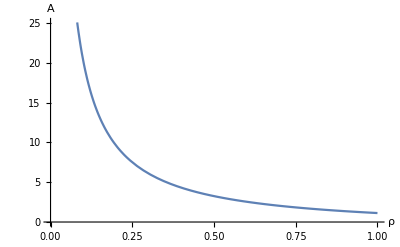

```mathematica
Plot[A[τ, π/2,ρ],{ρ, 0, 1},AxesLabel->{"ρ","A"}]
```

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMCunit[ϕ_] :=1+1/(2 ϕ^2)
```

Check This should be equal to Equation (1) for θ=π/2, β=0 and ρ=1:

```mathematica
FullSimplify[AHMCunit[ϕ]==F[0, ϕ, π/2, 1, r]]
```

True

## Inverse Laplace Transforms: Regular GHMC Autocorrelations

Inverting the autocorrelation functions gets very messy and so starting in reverse order now makes more sense, leaving the most complicated for last.

There is a sepcific method provided in the paper however, partial fraction decomposition is not well supported in Mathematica so it makes more sense to simply force the result for those that are no immediately obvious.

## HMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMCunit = InverseLaplaceTransform[FHMCunit[β ,ϕ, r],β,t] //ToRadicals // FullSimplify
```

(2 ⅇ^(1/3 t (-2 r+(r^2 (1-12 ϕ^2))/((r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3))+(r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3))) (3 √3 r^5 ϕ^2 (2-13 ϕ^2+64 ϕ^4)+r^2 (1+9 ϕ^2) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4))+√3 r^4 ϕ^2 (4-13 ϕ^2) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3)+r (1+3 ϕ^2) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3)+2 √3 r^3 ϕ^2 (1+2 ϕ^2) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(2/3)+√(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(2/3))+ⅇ^(1/6 t (-4 r+((1-ⅈ √3) r^2 (-1+12 ϕ^2))/((r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3))+(-1-ⅈ √3) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3))) (6 √3 r^5 ϕ^2 (2-13 ϕ^2+64 ϕ^4)+2 r^2 (1+9 ϕ^2) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4))+(3 ⅈ+√3) r^4 ϕ^2 (-4+13 ϕ^2) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3)-ⅈ (-ⅈ+√3) r (1+3 ϕ^2) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3)-2 (-3 ⅈ+√3) r^3 ϕ^2 (1+2 ϕ^2) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(2/3)+ⅈ (ⅈ+√3) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(2/3))+ⅇ^(1/6 t (-4 r+((1+ⅈ √3) r^2 (-1+12 ϕ^2))/((r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3))+ⅈ (ⅈ+√3) (r^3+9 r^3 ϕ^2+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3))) (6 √3 r^5 ϕ^2 (2-13 ϕ^2+64 ϕ^4)+2 r^2 (1+9 ϕ^2) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4))+(-3 ⅈ+√3) r^4 ϕ^2 (-4+13 ϕ^2) (r^3 (1+9 ϕ^2)+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3)+ⅈ (ⅈ+√3) r (1+3 ϕ^2) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)) (r^3 (1+9 ϕ^2)+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(1/3)-2 (3 ⅈ+√3) r^3 ϕ^2 (1+2 ϕ^2) (r^3 (1+9 ϕ^2)+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(2/3)+(-1-ⅈ √3) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)) (r^3 (1+9 ϕ^2)+3 √3 √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4)))^(2/3)))/(2 √3 r (9 r^3 ϕ^2 (2-13 ϕ^2+64 ϕ^4)+√3 (1+9 ϕ^2) √(r^6 ϕ^2 (2-13 ϕ^2+64 ϕ^4))))

```mathematica
CHMCunit[t_, ϕ_,r_ ] := Evaluate[iFHMCunit]
```

Plotting shows the underdamped form for unit mass and averge trajector length τ,

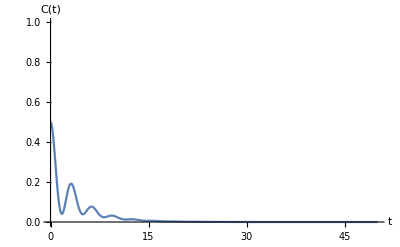

```mathematica
Plot[CHMCunit[t, τ, 1/τ], {t, 0, 50},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]
```

### HMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMC = InverseLaplaceTransform[FHMC[β ,ϕ,  ρ, r],β,t] //ToRadicals //FullSimplify
```

(-2 ⅇ^(1/3 t (-2 r+(r^2 (1-12 ϕ^2))/((r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3))+(r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3))) (-3 √3 r^5 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)+r^2 (-1+9 (-4+3 ρ) ϕ^2) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4))+√3 r^4 ϕ^2 (4 (-2+ρ)+(-32+9 (8-3 ρ) ρ) ϕ^2) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3)+r (-1+3 (-4+3 ρ) ϕ^2) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3)+2 √3 r^3 ϕ^2 (-2+ρ+2 (-4+3 ρ) ϕ^2) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(2/3)-√(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(2/3))-ⅇ^(1/6 t (-4 r+((1-ⅈ √3) r^2 (-1+12 ϕ^2))/((r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3))+(-1-ⅈ √3) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3))) (-6 √3 r^5 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)+2 r^2 (-1+9 (-4+3 ρ) ϕ^2) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4))+(3 ⅈ+√3) r^4 ϕ^2 (8-4 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3)-ⅈ (-ⅈ+√3) r (-1+3 (-4+3 ρ) ϕ^2) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3)-2 (-3 ⅈ+√3) r^3 ϕ^2 (-2+ρ+2 (-4+3 ρ) ϕ^2) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(2/3)+(1-ⅈ √3) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(2/3))-ⅇ^(1/6 t (-4 r+((1+ⅈ √3) r^2 (-1+12 ϕ^2))/((r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3))+ⅈ (ⅈ+√3) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3))) (-6 √3 r^5 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)+2 r^2 (-1+9 (-4+3 ρ) ϕ^2) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4))+(-3 ⅈ+√3) r^4 ϕ^2 (8-4 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3)+ⅈ (ⅈ+√3) r (-1+3 (-4+3 ρ) ϕ^2) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(1/3)-2 (3 ⅈ+√3) r^3 ϕ^2 (-2+ρ+2 (-4+3 ρ) ϕ^2) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(2/3)+(1+ⅈ √3) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)) (r^3 (1+9 (4-3 ρ) ϕ^2)+3 √3 √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)))^(2/3)))/(2 √3 r (9 r^3 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4)+√3 (1+9 (4-3 ρ) ϕ^2) √(r^6 ϕ^2 (4-2 ρ+(32+9 ρ (-8+3 ρ)) ϕ^2+64 ϕ^4))))

```mathematica
CHMC[t_, ϕ_, ρ_, r_ ] := Evaluate[iFHMC]
```

Plotting for varying acceptance rate at t=0,

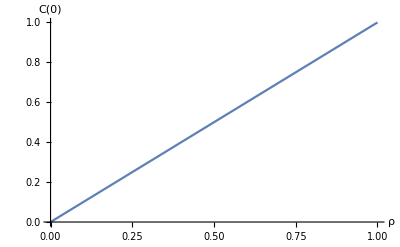

```mathematica
Plot[CHMC[0, τ, 1/τ, ρ], {ρ, 0, 1},PlotRange->{0,1},AxesLabel->{"ρ","C(0)"}]
```

## GHMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFunit = InverseLaplaceTransform[Funit[β, ϕ, θ, r],β,t] //ToRadicals // FullSimplify
```

$Aborted

```mathematica
Cunit[t_, ϕ_, θ_, r_] := Evaluate[iFunit]
```

varying with mixing angle θ,

```mathematica
Plot3D[Cunit[t,τ,θ,1/τ],{t,0,50},{θ,0.15π,2 π-0.15π},PlotTheme->"Scientific",PlotRange->{0,1},AxesLabel->{"t","θ","C(t)"}]
```

### GHMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iF = InverseLaplaceTransform[F[β, ϕ, θ,  ρ, r],β,t] //ToRadicals // FullSimplify
```

```mathematica
CF[t_, ϕ_, θ_,  ρ_, r_] := Evaluate[iF]
```

varying with mixing angle θ and acceptance probability,

```mathematica
Plot3D[CF[t,τ,π/4,1/τ,ρ ],{t,0,50},{ρ ,0.6,1},PlotTheme->"Scientific",PlotRange->{0,1},AxesLabel->{"t","ρ","C(t)"}]
```

```mathematica
DumpSave["dump.mx", "Global`"]
```